# Integration Rules for ∫(sin^j(z))^m(A+B sin^k(z))(a+b sin^k(z))^n ⅆz when j^2=1∧k^2=1∧a^2=b^2

Domain Map

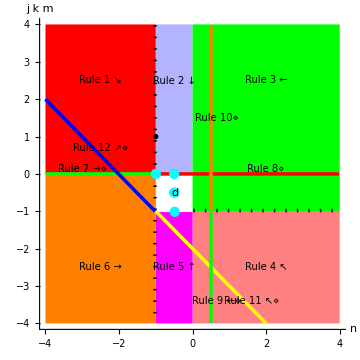

Legend:
•  The rule number in a colored region indicates the rule to use for integrals in that region.
•  The rule number next to a colored line indicates the rule to use for integrals on that line.
•  A white region or line indicates there is no rule for integrals in that region or on that line.
•  A solid black line indicates integrals on that line are handled by rules in another section.
•  A dashed black line on the border of a region indicates integrals on that border are handled by the rule for that region.
•  The arrow(s) following a rule number indicates the direction the rule drives integrands in the n×m exponent plane.
•  A ⋄ following a rule number indicates the rule transforms the integrand into a form handled by another section.
•  A red (stop) disk indicates the terminal rule to use for the point at the center of the disk.
•  A cyan disk indicates the non-terminal rule to use for the point at the center of the disk.

# Integration Rules for ∫(A+B sin^k(z))(a+b sin^k(z))^n ⅆz when k^2=1∧a^2=b^2

Rule a:  ∫(A+B Csc[c+d x])/(a+b Csc[c+d x])ⅆx

#### Derivation: Algebraic expansion

#### Basis: (A+B z)/(a+b z)=A/a-((b A-a B)z)/(a(a+b z))

#### Note: The rule for integrands of the same form when a^2-b^2≠0 could subsume this rule, but the resulting antiderivative will look less like the integrand involving sines instead of cosecants.

#### Rule a: If a^2-b^2=0 ∧ b A-a B≠0, then

∫(A+B Csc[c+d x])/(a+b Csc[c+d x])ⅆx  ⟶  (A x)/a-(b A-a B)/a∫Csc[c+d x]/(a+b Csc[c+d x])ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_]^(-1))/(a_+b_.*sin[c_.+d_.*x_]^(-1)),x_Symbol] :=
  A*x/a - Dist[(b*A-a*B)/a,Int[sin[c+d*x]^(-1)/(a+b*sin[c+d*x]^(-1)),x]] /;
FreeQ[{a,b,c,d,A,B},x] && ZeroQ[a^2-b^2] && NonzeroQ[b*A-a*B]
```

Rules 13-14:  ∫(A+B Csc[c+d x])(a+b Csc[c+d x])^n ⅆx

#### Derivation: Rule 6 with m=0 and k=-1

#### Rule 13: If a^2-b^2=0 ∧ b A-a B≠0 ∧ n<-1, then

∫(A+B Csc[c+d x]) (a+b Csc[c+d x])^n ⅆx  ⟶  -((b A-a B) Cot[c+d x](a+b Csc[c+d x])^n)/(b d (2n+1))+
1/(b^2(2n+1)) ∫(a A(2 n+1)-(b A-a B)(n+1)Csc[c+d x])(a+b Csc[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_]^(-1))*(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  -(b*A-a*B)*Cot[c+d*x]*(a+b*Csc[c+d*x])^n/(b*d*(2*n+1)) + 
  Dist[1/(b^2*(2*n+1)),
    Int[Sim[a*A*(2*n+1)-((b*A-a*B)*(n+1))*sin[c+d*x]^(-1),x]*(a+b*sin[c+d*x]^(-1))^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B},x] && ZeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && RationalQ[n] && n<-1
```

#### Derivation: Rule 3 with m=0 and k=-1

#### Rule 14: If a^2-b^2=0 ∧ b A-a B≠0 ∧ n>0, then

∫(A+B Csc[c+d x]) (a+b Csc[c+d x])^n ⅆx  ⟶  -(b B Cot[c+d x](a+b Csc[c+d x])^(n-1))/(d n)+
1/n ∫(a A n+(a B(2 n-1)+b A n)Csc[c+d x])(a+b Csc[c+d x])^(n-1)ⅆx

#### Program code:

```mathematica
Int[(A_+B_.*sin[c_.+d_.*x_]^(-1))*(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  -b*B*Cot[c+d*x]*(a+b*Csc[c+d*x])^(n-1)/(d*n) + 
  Dist[1/n,
    Int[Sim[a*A*n+(a*B*(2*n-1)+b*A*n)*sin[c+d*x]^(-1),x]*(a+b*sin[c+d*x]^(-1))^(n-1),x]] /;
FreeQ[{a,b,c,d,A,B},x] && ZeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && RationalQ[n] && n>0
```

# Integration Rules for ∫(sin^j(z))^m(A+B sin^k(z))(a+b sin^k(z))^n ⅆz when j^2=1∧k^2=1∧a^2=b^2

Rule c:  ∫(A+B Sin[c+d x]^k)/(Sin[c+d x]^((k+1)/2)√(a+b Sin[c+d x]^k))ⅆx

#### Derivation: Algebraic expansion

#### Basis: (A+B z^k)/(z^((k+1)/2)√(a+b z^k))=(A √(a+b z^k))/(a z^((k+1)/2))-((b A-a B)z^((k-1)/2))/(a √(a+b z^k))

#### Rule c: If k^2=1 ∧ a^2-b^2=0 ∧ b A-a B≠0, then

∫(A+B Sin[c+d x]^k)/(Sin[c+d x]^((k+1)/2)√(a+b Sin[c+d x]^k))ⅆx  ⟶  A/a∫(√(a+b Sin[c+d x]^k))/Sin[c+d x]^((k+1)/2)ⅆx-(b A-a B)/a∫Sin[c+d x]^((k-1)/2)/(√(a+b Sin[c+d x]^k))ⅆx

#### Program code:

```mathematica
Int[(A_+B_.*sin[c_.+d_.*x_])/(sin[c_.+d_.*x_]*Sqrt[a_+b_.*sin[c_.+d_.*x_]]),x_Symbol] :=
  Dist[A/a,Int[Sqrt[a+b*sin[c+d*x]]/sin[c+d*x],x]] - 
  Dist[(a*A-b*B)/b,Int[1/Sqrt[a+b*sin[c+d*x]],x]] /;
FreeQ[{a,b,c,d,A,B},x] && ZeroQ[a^2-b^2] && NonzeroQ[b*A-a*B]
```

```mathematica
Int[(A_+B_.*sin[c_.+d_.*x_]^(-1))/Sqrt[a_+b_.*sin[c_.+d_.*x_]^(-1)],x_Symbol] :=
  A/a*Int[Sqrt[a+b*sin[c+d*x]^(-1)],x] - 
  (b*A-a*B)/a*Int[sin[c+d*x]^(-1)/Sqrt[a+b*sin[c+d*x]^(-1)],x] /;
FreeQ[{a,b,c,d,A,B},x] && ZeroQ[a^2-b^2] && NonzeroQ[b*A-a*B]
```

Rule d:  ∫(A+B Sin[c+d x])/(√Sin[c+d x] √(a+b Sin[c+d x]))ⅆx

#### Derivation: Algebraic expansion

#### Rule d: If a^2-b^2=0 ∧ b A-a B≠0, then

∫(A+B Sin[c+d x])/(√Sin[c+d x] √(a+b Sin[c+d x]))ⅆx  ⟶  
B/b∫(√(a+b Sin[c+d x]))/(√Sin[c+d x])ⅆx+(b A-a B)/b∫1/(√Sin[c+d x]√(a+b Sin[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(A_+B_.*sin[c_.+d_.*x_])/(Sqrt[sin[c_.+d_.*x_]]*Sqrt[a_+b_.*sin[c_.+d_.*x_]]),x_Symbol] :=
  Dist[B/b,Int[Sqrt[a+b*sin[c+d*x]]/Sqrt[sin[c+d*x]],x]] + 
  Dist[(b*A-a*B)/b,Int[1/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x]] /;
FreeQ[{a,b,c,d,A,B},x] && ZeroQ[a^2-b^2] && NonzeroQ[b*A-a*B]
```

∫(Sin[c+d x]^j)^(m/2)(A+B Csc[c+d x])(a+b Csc[c+d x])^(n/2)ⅆx

#### Derivation: Rule 4 with j m=1/2, k=-1 and n=1/2

#### Rule: If j^2=1 ∧ a^2-b^2=0 ∧ j m=1/2, then

∫(Sin[c+d x]^j)^m(A+B Csc[c+d x])√(a+b Csc[c+d x])ⅆx  ⟶  
-(2a A Cos[c+d x])/(d(Sin[c+d x]^j)^m √(a+b Csc[c+d x]))+B∫(√(a+b Csc[c+d x]))/((Sin[c+d x]^j)^m)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(A_+B_.*sin[c_.+d_.*x_]^(-1))*Sqrt[a_+b_.*sin[c_.+d_.*x_]^(-1)],x_Symbol] :=
  -2*a*A*Cos[c+d*x]/(d*(Sin[c+d*x]^j)^m*Sqrt[a+b*Csc[c+d*x]]) + 
  Dist[B,Int[Sqrt[a+b*sin[c+d*x]^(-1)]/(sin[c+d*x]^j)^m,x]] /;
FreeQ[{a,b,c,d,A,B},x] && OneQ[j^2] && ZeroQ[a^2-b^2] && RationalQ[m] && j*m==1/2
```

#### Derivation: Algebraic expansion

#### Basis: (A+B z)/(√(a+b z))=(B √(a+b z))/b+(b A-a B)/(b √(a+b z))

#### Rule: If j^2=1 ∧ a^2-b^2=0 ∧ j m=-1/2 ∧ b A-a B≠0, then

∫((Sin[c+d x]^j)^m(A+B Csc[c+d x]))/(√(a+b Csc[c+d x]))ⅆx  ⟶  
B/b∫(sin[c+d x]^j)^m √(a+b Csc[c+d x]) ⅆx+(b A-a B)/b∫((Sin[c+d x]^j)^m)/(√(a+b Csc[c+d x])) ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(A_.+B_.*sin[c_.+d_.*x_]^(-1))/Sqrt[a_+b_.*sin[c_.+d_.*x_]^(-1)],x_Symbol] :=
  Dist[B/b,Int[(sin[c+d*x]^j)^m*Sqrt[a+b*sin[c+d*x]^(-1)],x]] + 
  Dist[(b*A-a*B)/b,Int[(sin[c+d*x]^j)^m/Sqrt[a+b*sin[c+d*x]^(-1)],x]] /;
FreeQ[{a,b,c,d,A,B},x] && OneQ[j^2] && ZeroQ[a^2-b^2] && RationalQ[m] && j*m==-1/2 && 
  NonzeroQ[b*A-a*B]
```

#### Derivation: Rule 5 with j m=1/2, k=-1 and n=-1/2

#### Rule: If j^2=1 ∧ a^2-b^2=0 ∧ j m=1/2 ∧ b A-a B≠0, then

∫((Sin[c+d x]^j)^m (A+B Csc[c+d x]))/(√(a+b Csc[c+d x]))ⅆx  ⟶  
-(2A Cos[c+d x])/(d(Sin[c+d x]^j)^m √(a+b Csc[c+d x]))-(b A-a B)/a ∫1/((Sin[c+d x]^j)^m √(a+b Csc[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(A_+B_.*sin[c_.+d_.*x_]^(-1))/Sqrt[a_+b_.*sin[c_.+d_.*x_]^(-1)],x_Symbol] :=
  -2*A*Cos[c+d*x]/(d*(Sin[c+d*x]^j)^m*Sqrt[a+b*Csc[c+d*x]]) - 
  Dist[(b*A-a*B)/a,Int[1/((sin[c+d*x]^j)^m*Sqrt[a+b*sin[c+d*x]^(-1)]),x]] /;
FreeQ[{a,b,c,d,A,B},x] && OneQ[j^2] && ZeroQ[a^2-b^2] && RationalQ[m] && j*m==1/2 && 
  NonzeroQ[b*A-a*B]
```

Rules 9-10:  ∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k)√(a+b Sin[c+d x]^k)ⅆx

#### Derivation: Rule 4 with n=1/2 and a B (j k m+(k+1)/2)+b A (j k m+(k+2)/2)=0

#### Derivation: Rule 3 with n=1/2 and a B (j k m+(k+1)/2)+b A (j k m+(k+2)/2)=0

#### Rule 9a: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ b A-a B≠0 ∧ j k m+(k+1)/2≠0 ∧ a B (j k m+(k+1)/2)+b A (j k m+(k+2)/2)=0, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k)√(a+b Sin[c+d x]^k)ⅆx  ⟶  (a A Cos[c+d x] (Sin[c+d x]^j)^(m+j k))/(d(j k m+(k+1)/2)√(a+b Sin[c+d x]^k))

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(A_.+B_.*sin[c_.+d_.*x_]^k_.)*Sqrt[a_+b_.*sin[c_.+d_.*x_]^k_.],x_Symbol] :=
  a*A*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)/(d*(j*k*m+(k+1)/2)*Sqrt[a+b*Sin[c+d*x]^k]) /;
FreeQ[{a,b,c,d,A,B,m},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && 
  NonzeroQ[j*k*m+(k+1)/2] && ZeroQ[a*B*(j*k*m+(k+1)/2)+b*A*(j*k*m+(k+2)/2)]
```

#### Derivation: Rule 4 with n=1/2

#### Rule 9b: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ b A-a B≠0 ∧ j k m+(k+1)/2≠0 ∧ j k m≤-1 ∧ a B (j k m+(k+1)/2)+b A (j k m+(k+2)/2)≠0, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k)√(a+b Sin[c+d x]^k)ⅆx  ⟶  (a A Cos[c+d x] (Sin[c+d x]^j)^(m+j k))/(d(j k m+(k+1)/2)√(a+b Sin[c+d x]^k))+
(a B (j k m+(k+1)/2)+b A (j k m+(k+2)/2))/(a(j k m+(k+1)/2))∫(Sin[c+d x]^j)^(m+j k)√(a+b Sin[c+d x]^k)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+B_.*sin[c_.+d_.*x_]^k_.)*Sqrt[a_+b_.*sin[c_.+d_.*x_]^k_.],x_Symbol] :=
  a*A*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)/(d*(j*k*m+(k+1)/2)*Sqrt[a+b*Sin[c+d*x]^k]) + 
  Dist[(a*B*(j*k*m+(k+1)/2)+b*A*(j*k*m+(k+2)/2))/(a*(j*k*m+(k+1)/2)),
    Int[(sin[c+d*x]^j)^(m+j*k)*Sqrt[a+b*sin[c+d*x]^k],x]] /;
FreeQ[{a,b,c,d,A,B},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && 
  RationalQ[m] && NonzeroQ[j*k*m+(k+1)/2] && j*k*m≤-1 && 
  NonzeroQ[a*B*(j*k*m+(k+1)/2)+b*A*(j*k*m+(k+2)/2)]
```

#### Derivation: Rule 3 with n=1/2

#### Rule 10: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ b A-a B≠0 ∧ j k m+(k+2)/2≠0 ∧ j k m≥-1 ∧ a B (j k m+(k+1)/2)+b A (j k m+(k+2)/2)≠0, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k)√(a+b Sin[c+d x]^k)ⅆx  ⟶  -(b B Cos[c+d x] (Sin[c+d x]^j)^(m+j k))/(d(j k m+(k+2)/2)√(a+b Sin[c+d x]^k))+
(a B (j k m+(k+1)/2)+b A (j k m+(k+2)/2))/(b(j k m+(k+2)/2))∫(Sin[c+d x]^j)^m √(a+b Sin[c+d x]^k)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(A_.+B_.*sin[c_.+d_.*x_]^k_.)*Sqrt[a_+b_.*sin[c_.+d_.*x_]^k_.],x_Symbol] :=
  -b*B*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)/(d*(j*k*m+(k+2)/2)*Sqrt[a+b*Sin[c+d*x]^k]) + 
  Dist[(a*B*(j*k*m+(k+1)/2)+b*A*(j*k*m+(k+2)/2))/(b*(j*k*m+(k+2)/2)),
    Int[(sin[c+d*x]^j)^m*Sqrt[a+b*sin[c+d*x]^k],x]] /;
FreeQ[{a,b,c,d,A,B},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && 
  RationalQ[m] && NonzeroQ[j*k*m+(k+2)/2] && j*k*m≥-1 && 
  NonzeroQ[a*B*(j*k*m+(k+1)/2)+b*A*(j*k*m+(k+2)/2)]
```

Rules 11-12:  ∫((Sin[c+d x]^j)^m (A+B Sin[c+d x]^k))/((a+b Sin[c+d x]^k)^(j k m+(k+3)/2))ⅆx

#### Derivation: Rule 5 with j k m+n+(k+3)/2=0 and a B(n+1)+b A n=0

#### Rule 11a: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ b A-a B≠0 ∧ j k m+n+(k+3)/2=0 ∧ n+1≠0 ∧ a B(n+1)+b A n=0, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(A Cos[c+d x] (Sin[c+d x]^j)^(m+j k) (a+b Sin[c+d x]^k)^n)/(d(n+1))

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(A_.+B_.*sin[c_.+d_.*x_]^k_.)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -A*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^n/(d*(n+1)) /;
FreeQ[{a,b,c,d,A,B,m,n},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && 
  ZeroQ[j*k*m+n+(k+3)/2] && NonzeroQ[n+1] && ZeroQ[a*B*(n+1)+b*A*n]
```

#### Derivation: Rule 5 with j k m+n+(k+3)/2=0

#### Rule 11b: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ b A-a B≠0 ∧ j k m+n+(k+3)/2=0 ∧ n>-1 ∧ a B(n+1)+b A n≠0, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(A Cos[c+d x] (Sin[c+d x]^j)^(m+j k) (a+b Sin[c+d x]^k)^n)/(d(n+1))+
(a B(n+1)+b A n)/(a(n+1))∫(Sin[c+d x]^j)^(m+j k)(a+b Sin[c+d x]^k)^n ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(A_.+B_.*sin[c_.+d_.*x_]^k_.)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -A*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^n/(d*(n+1)) + 
  Dist[(a*B*(n+1)+b*A*n)/(a*(n+1)),Int[(sin[c+d*x]^j)^(m+j*k)*(a+b*sin[c+d*x]^k)^n,x]] /;
FreeQ[{a,b,c,d,A,B},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && 
  RationalQ[m,n] && ZeroQ[j*k*m+n+(k+3)/2] && n>-1 && NonzeroQ[a*B*(n+1)+b*A*n]
```

#### Derivation: Rule 6 with j k m+n+(k+3)/2=0 and b B(n+1)+a A n=0

#### Rule 12a: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ b A-a B≠0 ∧ j k m+n+(k+3)/2=0 ∧ 2n+1≠0 ∧ b B(n+1)+a A n=0, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-((b A-a B) Cos[c+d x](Sin[c+d x]^j)^(m+j k)(a+b Sin[c+d x]^k)^n)/(b d (2n+1))

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(A_.+B_.*sin[c_.+d_.*x_]^k_.)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -(b*A-a*B)*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^n/(b*d*(2*n+1)) /;
FreeQ[{a,b,c,d,A,B,m,n},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && 
  ZeroQ[j*k*m+n+(k+3)/2] && NonzeroQ[2*n+1] && ZeroQ[b*B*(n+1)+a*A*n]
```

#### Derivation: Rule 6 with j k m+n+(k+3)/2=0

#### Rule 12b: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ b A-a B≠0 ∧ j k m+n+(k+3)/2=0 ∧ n≤-1 ∧ b B(n+1)+a A n≠0, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-((b A-a B) Cos[c+d x](Sin[c+d x]^j)^(m+j k)(a+b Sin[c+d x]^k)^n)/(b d (2n+1))+
(b B(n+1)+a A n)/(a^2(2n+1)) ∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(A_.+B_.*sin[c_.+d_.*x_]^k_.)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -(b*A-a*B)*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^n/(b*d*(2*n+1)) + 
  Dist[(b*B*(n+1)+a*A*n)/(a^2*(2*n+1)),Int[(sin[c+d*x]^j)^m*(a+b*sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && 
  RationalQ[m,n] && ZeroQ[j*k*m+n+(k+3)/2] && n≤-1 && NonzeroQ[b*B*(n+1)+a*A*n]
```

Rules 7-8:  ∫Sin[c+d x]^((k-1)/2)(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx

#### Derivation: Rule 2 with j m=(k-1)/2 and a B n+b A(n+1)=0

#### Rule: If k^2=1 ∧ a^2-b^2=0 ∧ a B n+b A (n+1)=0 , then

∫Sin[c+d x]^((k-1)/2)(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(B Cos[c+d x]Sin[c+d x]^((k-1)/2)(a+b Sin[c+d x]^k)^n)/(d(n+1))

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_])*(a_+b_.*sin[c_.+d_.*x_])^n_.,x_Symbol] :=
  -B*Cos[c+d*x]*(a+b*Sin[c+d*x])^n/(d*(n+1)) /;
FreeQ[{a,b,c,d,A,B,n},x] && ZeroQ[a^2-b^2] && ZeroQ[a*B*n+b*A*(n+1)]
```

```mathematica
Int[sin[c_.+d_.*x_]^(-1)*(A_+B_.*sin[c_.+d_.*x_]^(-1))*(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_.,x_Symbol] :=
  -B*Cot[c+d*x]*(a+b*Csc[c+d*x])^n/(d*(n+1)) /;
FreeQ[{a,b,c,d,A,B,n},x] && ZeroQ[a^2-b^2] && ZeroQ[a*B*n+b*A*(n+1)]
```

#### Derivation: Rule 1 with j m=(k-1)/2

#### Rule 7: If k^2=1 ∧ a^2-b^2=0 ∧ b A-a B≠0 ∧ n≤-1 ∧ a B n+b A (n+1)≠0, then

∫Sin[c+d x]^((k-1)/2)(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
((b A-a B) Cos[c+d x]Sin[c+d x]^((k-1)/2)(a+b Sin[c+d x]^k)^n)/(a d (2n+1))+
(a B n+b A(n+1))/(a b(2n+1))∫Sin[c+d x]^((k-1)/2)(a+b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_])*(a_+b_.*sin[c_.+d_.*x_])^n_,x_Symbol] :=
  (b*A-a*B)*Cos[c+d*x]*(a+b*Sin[c+d*x])^n/(a*d*(2*n+1)) + 
  Dist[(a*B*n+b*A*(n+1))/(a*b*(2*n+1)),Int[(a+b*sin[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B},x] && ZeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && RationalQ[n] && n≤-1 && 
  NonzeroQ[a*B*n+b*A*(n+1)]
```

```mathematica
Int[sin[c_.+d_.*x_]^(-1)*(A_+B_.*sin[c_.+d_.*x_]^(-1))*(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  (b*A-a*B)*Cot[c+d*x]*(a+b*Csc[c+d*x])^n/(a*d*(2*n+1)) + 
  Dist[(a*B*n+b*A*(n+1))/(a*b*(2*n+1)),Int[sin[c+d*x]^(-1)*(a+b*sin[c+d*x]^(-1))^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B},x] && ZeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && RationalQ[n] && n≤-1 && 
  NonzeroQ[a*B*n+b*A*(n+1)]
```

#### Derivation: Rule 2 with j m=(k-1)/2

#### Rule 8: If k^2=1 ∧ a^2-b^2=0 ∧ b A-a B≠0 ∧ n>-1 ∧ n≠1 ∧ a B n+b A (n+1)≠0 , then

∫Sin[c+d x]^((k-1)/2)(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(B Cos[c+d x]Sin[c+d x]^((k-1)/2)(a+b Sin[c+d x]^k)^n)/(d(n+1))+
(a B n+b A (n+1))/(b (n+1))∫ Sin[c+d x]^((k-1)/2)(a+b Sin[c+d x]^k)^n ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_])*(a_+b_.*sin[c_.+d_.*x_])^n_,x_Symbol] :=
  -B*Cos[c+d*x]*(a+b*Sin[c+d*x])^n/(d*(n+1)) + 
  Dist[(a*B*n+b*A*(n+1))/(b*(n+1)),Int[(a+b*sin[c+d*x])^n,x]] /;
FreeQ[{a,b,c,d,A,B},x] && ZeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && RationalQ[n] && 
  n>-1 && n≠1 && NonzeroQ[a*B*n+b*A*(n+1)]
```

```mathematica
Int[sin[c_.+d_.*x_]^(-1)*(A_+B_.*sin[c_.+d_.*x_]^(-1))*(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  -B*Cot[c+d*x]*(a+b*Csc[c+d*x])^n/(d*(n+1)) + 
  Dist[(a*B*n+b*A*(n+1))/(b*(n+1)),Int[sin[c+d*x]^(-1)*(a+b*sin[c+d*x]^(-1))^n,x]] /;
FreeQ[{a,b,c,d,A,B},x] && ZeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && RationalQ[n] && 
  n>-1 && n≠1 && NonzeroQ[a*B*n+b*A*(n+1)]
```

Rules 1-6:  ∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx

#### Derivation: Recurrence 7

#### Rule 1: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ b A-a B≠0 ∧ j k m>0 ∧ n≤-1, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
((b A-a B) Cos[c+d x] (Sin[c+d x]^j)^m (a+b Sin[c+d x]^k)^n)/(a d (2n+1))+
1/(a^2 (2n+1))∫(Sin[c+d x]^j)^(m-j k)·
(-(b A-a B)(j k m+(k-1)/2)+(b B n+a A (n+1)+(a A-b B)(j k m+(k-1)/2))Sin[c+d x]^k)(a+b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+B_.*sin[c_.+d_.*x_]^k_.)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  (b*A-a*B)*Cos[c+d*x]*(Sin[c+d*x]^j)^m*(a+b*Sin[c+d*x]^k)^n/(a*d*(2*n+1)) + 
  Dist[1/(a^2*(2*n+1)),
    Int[(sin[c+d*x]^j)^(m-j*k)*
      Sim[-(b*A-a*B)*(j*k*m+(k-1)/2)+(b*B*n+a*A*(n+1)+(a*A-b*B)*(j*k*m+(k-1)/2))*sin[c+d*x]^k,x]*
      (a+b*sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && 
  RationalQ[m,n] && j*k*m>0 && n≤-1 && Not[j*k*m==1 && n==-1]
```

#### Derivation: Recurrence 8

#### Rule 2: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ b A-a B≠0 ∧ j k m+n+(k+1)/2≠0 ∧ j k m>0 ∧ -1<n<0, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(B Cos[c+d x](Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^n)/(d (j k m+n+(k+1)/2))+
1/(a (j k m+n+(k+1)/2))∫(Sin[c+d x]^j)^(m-j k)·
(a B (j k m+(k-1)/2)+(b B n+a A(j k m+n+(k+1)/2))Sin[c+d x]^k)(a+b Sin[c+d x]^k)^n ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+B_.*sin[c_.+d_.*x_]^k_.)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -B*Cos[c+d*x]*(Sin[c+d*x]^j)^m*(a+b*Sin[c+d*x]^k)^n/(d*(j*k*m+n+(k+1)/2)) + 
  Dist[1/(a*(j*k*m+n+(k+1)/2)),
    Int[(sin[c+d*x]^j)^(m-j*k)*
      Sim[a*B*(j*k*m+(k-1)/2)+(b*B*n+a*A*(j*k*m+n+(k+1)/2))*sin[c+d*x]^k,x]*
      (a+b*sin[c+d*x]^k)^n,x]] /;
FreeQ[{a,b,c,d,A,B},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && 
  RationalQ[m,n] && NonzeroQ[j*k*m+n+(k+1)/2] && j*k*m>0 && -1<n<0 && Not[j*m==1 && k==1]
```

#### Derivation: Recurrence 9

#### Note: In the case n=1/2, this rule simplifies to rule 10.

#### Rule 3: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ b A-a B≠0 ∧ j k m+n+(k+1)/2≠0 ∧ j k m≥-1 ∧ n>0 ∧ n≠1/2, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(b B Cos[c+d x](Sin[c+d x]^j)^(m+j k)(a+b Sin[c+d x]^k)^(n-1))/(d (j k m+n+(k+1)/2))+
1/(j k m+n+(k+1)/2) ∫(Sin[c+d x]^j)^m·
(a A n+(a A+b B)(j k m+(k+1)/2)+(b A+a B n+(b A+a B)(j k m+n+(k-1)/2))Sin[c+d x]^k)(a+b Sin[c+d x]^k)^(n-1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+B_.*sin[c_.+d_.*x_]^k_.)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_.,x_Symbol] :=
  -b*B*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^(n-1)/(d*(j*k*m+n+(k+1)/2)) + 
  Dist[1/(j*k*m+n+(k+1)/2),
    Int[(sin[c+d*x]^j)^m*
      Sim[a*A*n+(a*A+b*B)*(j*k*m+(k+1)/2)+(b*A+a*B*n+(b*A+a*B)*(j*k*m+n+(k-1)/2))*sin[c+d*x]^k,x]*
      (a+b*sin[c+d*x]^k)^(n-1),x]] /;
FreeQ[{a,b,c,d,A,B},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && 
  RationalQ[m,n] && NonzeroQ[j*k*m+n+(k+1)/2] && j*k*m≥-1 && n>0 && n≠1/2 && Not[j*m==1 && k==1]
```

#### Derivation: Recurrence 10

#### Note: In the case n=1/2, this rule simplifies to rule 9b.

#### Rule 4: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ b A-a B≠0 ∧ j k m<-1 ∧ n>0 ∧ n≠1/2, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
(a A Cos[c+d x] (Sin[c+d x]^j)^(m+j k) (a+b Sin[c+d x]^k)^(n-1))/(d(j k m+(k+1)/2))+
1/(j k m+(k+1)/2)∫(Sin[c+d x]^j)^(m+j k)·
((b A+a B)(j k m+(k+1)/2)-b A (n-1)+(a A n+(a A+b B)(j k m+(k+1)/2)) Sin[c+d x]^k)(a+b Sin[c+d x]^k)^(n-1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+B_.*sin[c_.+d_.*x_]^k_.)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  a*A*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^(n-1)/(d*(j*k*m+(k+1)/2)) + 
  Dist[1/(j*k*m+(k+1)/2),
    Int[(sin[c+d*x]^j)^(m+j*k)*
      Sim[(b*A+a*B)*(j*k*m+(k+1)/2)-b*A*(n-1)+(a*A*n+(a*A+b*B)*(j*k*m+(k+1)/2))*sin[c+d*x]^k,x]*
      (a+b*sin[c+d*x]^k)^(n-1),x]] /;
FreeQ[{a,b,c,d,A,B},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && 
  RationalQ[m,n] && j*k*m<-1 && n>0 && n≠1/2
```

#### Derivation: Recurrence 11

#### Rule 5: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ b A-a B≠0 ∧ j k m+(k+1)/2≠0 ∧ j k m≤-1 ∧ -1<n<0, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
(A Cos[c+d x] (Sin[c+d x]^j)^(m+j k) (a+b Sin[c+d x]^k)^n)/(d(j k m+(k+1)/2))+
1/(a(j k m+(k+1)/2))∫(Sin[c+d x]^j)^(m+j k)·
(a B(j k m+(k+1)/2)-b A n+a A(j k m+n+(k+3)/2) Sin[c+d x]^k)(a+b Sin[c+d x]^k)^n ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+B_.*sin[c_.+d_.*x_]^k_.)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_.,x_Symbol] :=
  A*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^n/(d*(j*k*m+(k+1)/2)) + 
  Dist[1/(a*(j*k*m+(k+1)/2)),
    Int[(sin[c+d*x]^j)^(m+j*k)*
      Sim[a*B*(j*k*m+(k+1)/2)-b*A*n+a*A*(j*k*m+n+(k+3)/2)*sin[c+d*x]^k,x]*
      (a+b*sin[c+d*x]^k)^n,x]] /;
FreeQ[{a,b,c,d,A,B},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && 
  RationalQ[m,n] && NonzeroQ[j*k*m+(k+1)/2] && j*k*m≤-1 && -1<n<0
```

#### Derivation: Recurrence 12

#### Rule 6: If j^2=k^2=1 ∧ a^2-b^2≠0 ∧ b A-a B≠0 ∧ j k m<0 ∧ n≤-1, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-((b A-a B) Cos[c+d x](Sin[c+d x]^j)^(m+j k)(a+b Sin[c+d x]^k)^n)/(b d (2n+1))+
1/(b^2(2n+1)) ∫(Sin[c+d x]^j)^m·
(a A(2 n+1)+(a A-b B)(j k m+(k+1)/2)-(b A-a B)(j k m+n+(k+3)/2)Sin[c+d x]^k)(a+b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+B_.*sin[c_.+d_.*x_]^k_.)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -(b*A-a*B)*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^n/(b*d*(2*n+1)) + 
  Dist[1/(b^2*(2*n+1)),
    Int[(sin[c+d*x]^j)^m*
      Sim[a*A*(2*n+1)+(a*A-b*B)*(j*k*m+(k+1)/2)-(b*A-a*B)*(j*k*m+n+(k+3)/2)*sin[c+d*x]^k,x]*
      (a+b*sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && 
  RationalQ[m,n] && j*k*m<0 && n≤-1
```